## QCD

### α

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs[2]
```

0.293951

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
αs[Mt]
```

0.107925

```mathematica
αsNf[Mb,5]
```

0.217151

```mathematica
αsNf[Mb,4]
```

0.215429

```mathematica
αsNf[Mc,4]
```

0.335937

```mathematica
αsNf[Mc,3]
```

0.322415

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,4],Mc≤Q<Mb},{αsNf4Loop[Q,5],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf4Loop[Mt,6]-(αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0897171

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf4Loop[Mb,4]-(αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.303565

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf4Loop[Mc,3]-(αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.378129

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335423

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.147643

```mathematica
αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}
```

0.206797

```mathematica
αsNf1Loop[Mb,4]/.{Λ->Λ1LoopNf4}
```

0.206797

```mathematica
αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}
```

0.301123

```mathematica
αsNf1Loop[Mc,3]/.{Λ->Λ1LoopNf3}
```

0.301123

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.297172

0.304349

0.319784

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1904.31

1860.69

3990.83

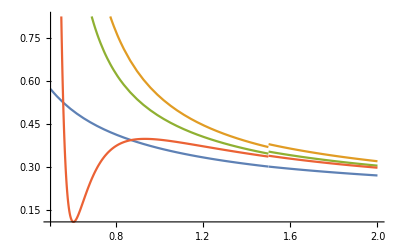

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

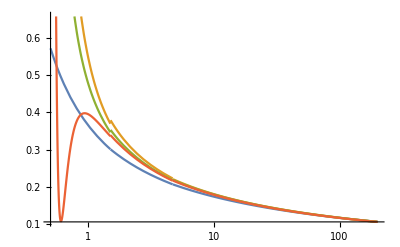

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.05254,3.74331,3.42818,3.1062,2.77611,2.43616,2.08379,1.715}

```mathematica
Nf4α1LoopMid=Table[αs1Loop[Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopStepTab=Round[4/(.2 Nf4α1LoopMid^2)]
```

{430,411,390,367,342,314,282,245}

```mathematica
Nf4α1LoopBig=Table[αs1Loop[1/2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.268835,0.276665,0.28589,0.296997,0.311546,0.330832,0.357283,0.396841}

```mathematica
Nf4α1LoopSmall=Table[αs1Loop[2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.181799,0.185058,0.188807,0.193197,0.198453,0.204935,0.213849,0.226354}

```mathematica
Length[DeleteDuplicates[Join[Nf4α1LoopMid,Nf4α1LoopBig,Nf4α1LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α1Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.1266,72.9651,62.6156,52.0329,41.1465,29.8326,17.822,4.05254}

```mathematica
Mt
```

173.34

```mathematica
Nf5α1LoopMid=Table[αs1Loop[Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopStepTab=Round[4/(.2 Nf5α1LoopMid^2)]
```

{1391,1339,1278,1207,1120,1006,835,430}

```mathematica
Nf5α1LoopBig=Table[αs1Loop[1/2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.133418,0.136311,0.13987,0.144434,0.150667,0.160132,0.178055,0.268835}

```mathematica
Nf5α1LoopSmall=Table[αs1Loop[2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.108852,0.11077,0.113109,0.116075,0.120067,0.126002,0.136841,0.181799}

```mathematica
Length[DeleteDuplicates[Join[Nf5α1LoopMid,Nf5α1LoopBig,Nf5α1LoopSmall]]]
```

24

```mathematica
Nf4α1LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α1LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α2Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α2LoopMid=Table[αs2Loop[Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopStepTab=Round[4/(.2 Nf4α2LoopMid^2)]
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf4α2LoopBig=Table[αs2Loop[1/2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall=Table[αs2Loop[2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.223621,0.238097}

```mathematica
Nf4α2LoopSmall[[-2]]=0.22362;
```

```mathematica
Length[DeleteDuplicates[Join[Nf4α2LoopMid,Nf4α2LoopBig,Nf4α2LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α2Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α2Loopμ/Nf5mQTab
```

{0.481523,0.491366,0.50345,0.518914,0.539976,0.571839,0.631796,0.917683}

```mathematica
2Nf5α2Loopμ/Nf5mQTab
```

{0.963046,0.982731,1.0069,1.03783,1.07995,1.14368,1.26359,1.83537}

```mathematica
1/2Nf5α2Loopμ/Nf5mQTab
```

{0.240762,0.245683,0.251725,0.259457,0.269988,0.285919,0.315898,0.458842}

```mathematica
Nf5α2LoopMid=Table[αs2Loop[Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopStepTab=Round[4/(.2 Nf5α2LoopMid^2)]
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α2LoopBig=Table[αs2Loop[1/2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall=Table[αs2Loop[2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Length[DeleteDuplicates[Join[Nf5α2LoopMid,Nf5α2LoopBig,Nf5α2LoopSmall]]]
```

24

```mathematica
Nf4α2LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α2LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NNLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α3Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.24177,3.9304,3.61282,3.28803,2.95474,2.61112,2.2546,1.88115}

```mathematica
Nf4α3LoopMid=Table[αs3Loop[Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopStepTab=Round[4/(.2 Nf4α3LoopMid^2)]
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α3LoopBig=Table[αs3Loop[1/2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.296093,0.306917,0.319941,0.336039,0.34972,0.380431,0.426678,0.508047}

```mathematica
Nf4α3LoopSmall=Table[αs3Loop[2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Length[DeleteDuplicates[Join[Nf4α3LoopMid,Nf4α3LoopBig,Nf4α3LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α3Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4695,73.3338,63.0043,52.434,41.5493,30.2209,18.1659,4.24177}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α3Loopμ/Nf5mQTab
```

{0.481536,0.491353,0.503401,0.518811,0.539782,0.571469,0.630948,0.902505}

```mathematica
2Nf5α3Loopμ/Nf5mQTab
```

{0.963073,0.982706,1.0068,1.03762,1.07956,1.14294,1.2619,1.80501}

```mathematica
1/2Nf5α3Loopμ/Nf5mQTab
```

{0.240768,0.245677,0.251701,0.259405,0.269891,0.285734,0.315474,0.451253}

```mathematica
Nf5α3LoopMid=Table[αs3Loop[Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopStepTab=Round[4/(.2 Nf5α3LoopMid^2)]
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf5α3LoopBig=Table[αs3Loop[1/2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.134841,0.137946,0.14178,0.146722,0.153516,0.163936,0.184024,0.296093}

```mathematica
Nf5α3LoopSmall=Table[αs3Loop[2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.108781,0.110771,0.113203,0.116293,0.120467,0.126701,0.138172,0.187113}

```mathematica
Length[DeleteDuplicates[Join[Nf5α3LoopMid,Nf5α3LoopBig,Nf5α3LoopSmall]]]
```

24

```mathematica
Nf4α3LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α3LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

### M_QQbar

```mathematica
datadir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
NWalkers=200;
```

```mathematica
<<MaTeX`
```

#### LO

```mathematica
Nf4α1LoopMid
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopBig]}]
```

{-0.0321210010,-0.0340193410,-0.0363258210,-0.0392032110,-0.0431381810,-0.0486443610,-0.0567338410,-0.0699923510}

```mathematica
Nf4α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopMid]}]
```

{-0.0206516110,-0.0216219410,-0.0227788610,-0.0241904110,-0.0259641710,-0.0282833910,-0.0314892110,-0.0363113410}

```mathematica
Nf4α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopSmall]}]
```

{-0.0146892810,-0.0152206510,-0.0158435910,-0.0165889210,-0.0175038210,-0.0186659410,-0.0203250610,-0.0227716110}

```mathematica
Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-0.444442622,-0.444446221,-0.444446220,-0.444446218,-0.444444517,-0.444445816,-0.444444214,-0.444445212}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

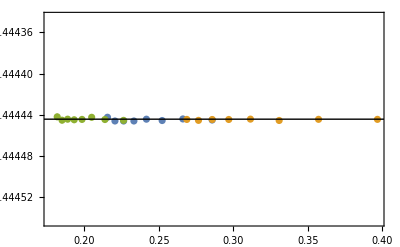

```mathematica
Show[ListPlot[{Reverse@Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqbarMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqbarBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqbarSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

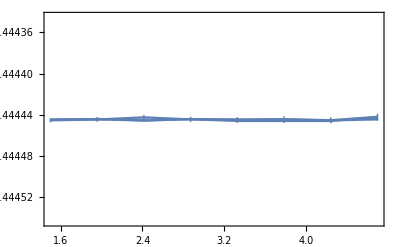

```mathematica
Nf4α1LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqbarMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqbarBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqbarSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{{Mc,Mb},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

```mathematica
Nf5α1LoopMid
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopBig]}]
```

{-0.0079112710,-0.0082580810,-0.0086949410,-0.0092716410,-0.0100891310,-0.0113965610,-0.0140904810,-0.0321210010}

```mathematica
Nf5α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopMid]}]
```

{-0.0063882710,-0.0066391010,-0.0069526710,-0.0073629010,-0.0079372710,-0.0088400110,-0.0106435010,-0.0206516110}

```mathematica
Nf5α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopSmall]}]
```

{-0.0052661110,-0.0054533310,-0.0056860610,-0.0059881810,-0.0064071510,-0.0070562210,-0.0083224310,-0.0146892810}

```mathematica
Nf5α1LoopΔEqqbarMid/Nf5α1LoopMid^2
```

{-0.4444487,-0.4444467,-0.4444456,-0.4444476,-0.4444436,-0.4444475,-0.4444464,-0.444442622}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

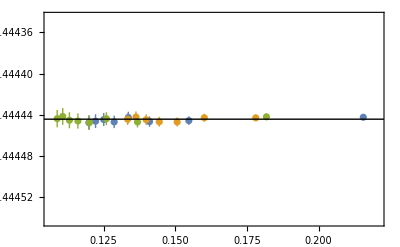

```mathematica
Show[ListPlot[{Reverse@Table[{Nf5α1LoopMid[[i]],Nf5α1LoopΔEqqbarMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopBig[[i]],Nf5α1LoopΔEqqbarBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopSmall[[i]],Nf5α1LoopΔEqqbarSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

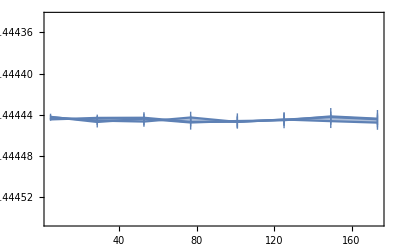

```mathematica
Nf5α1LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqbarMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqbarBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqbarSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{{Mb,Mt},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

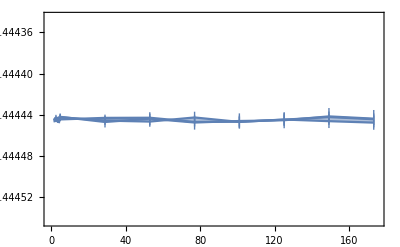

```mathematica
Show[Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{{Mc-2,Mt+2},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}}]
```

#### NLO

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopBig]}]
```

{-0.089390.00026,-0.097980.00026,-0.109890.00032,-0.128880.00030,-0.15130.0006,-0.18060.0007,-0.24560.0010,-0.40030.0011}

```mathematica
Nf4α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopMid]}]
```

{-0.054980.00028,-0.059540.00031,-0.062540.00033,-0.06990.0004,-0.07930.0005,-0.08960.0005,-0.10650.0007,-0.13800.0009}

```mathematica
Nf4α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopSmall]}]
```

{-0.037710.00026,-0.040170.00029,-0.042110.00032,-0.04550.0004,-0.04750.0004,-0.05270.0005,-0.05900.0005,-0.07190.0007}

```mathematica
Nf4α2LoopΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.0450.005,-1.0720.006,-1.0580.006,-1.1000.007,-1.1460.007,-1.1650.007,-1.2120.008,-1.3110.009}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf4α2LoopΔEqqbarBig/Nf4α2LoopBig^2
```

{-0.94580.0027,-0.95830.0026,-0.98080.0029,-1.03150.0024,-1.0600.004,-1.1060.004,-1.1550.005,-1.25410.0033}

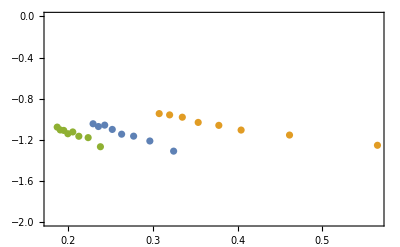

```mathematica
Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

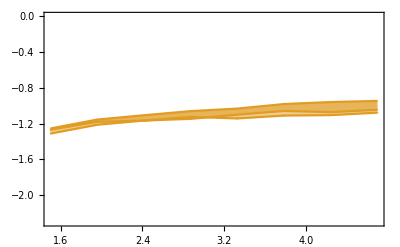

```mathematica
Nf4α2LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{-2.3,0}},Joined->True,Filling->{True},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

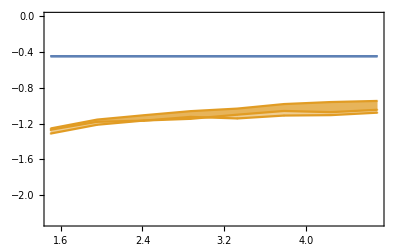

```mathematica
Show[Nf4α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot]
```

```mathematica
Nf5α2LoopMid
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopBig
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopBig
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.22362,0.238097}

```mathematica
Nf5α2Loopμ
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Nf4α2Loopμ
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf4α2LoopStepTab
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf5α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopBig]}]
```

{-0.0119740.000018,-0.0127670.000015,-0.0136070.000020,-0.0146490.000019,-0.0163330.000028,-0.0188180.000034,-0.025120.00004,-0.085850.00021}

```mathematica
Nf5α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopMid]}]
```

{-0.0105380.000024,-0.0106060.000026,-0.0115690.000027,-0.0124020.000032,-0.013160.00004,-0.015430.00004,-0.019460.00008,-0.050570.00026}

```mathematica
Nf5α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopSmall]}]
```

{-0.008880.00004,-0.0092160.000032,-0.0098140.000034,-0.010650.00004,-0.011360.00004,-0.012870.00005,-0.016280.00007,-0.035500.00025}

```mathematica
Nf4α2LoopΔEqqbarBig
```

{-0.089390.00026,-0.097980.00026,-0.109890.00032,-0.128880.00030,-0.15130.0006,-0.18060.0007,-0.24560.0010,-0.40030.0011}

```mathematica
Nf4α2LoopΔEqqbarMid
```

{-0.054980.00028,-0.059540.00031,-0.062540.00033,-0.06990.0004,-0.07930.0005,-0.08960.0005,-0.10650.0007,-0.13800.0009}

```mathematica
Nf4α2LoopΔEqqbarSmall
```

{-0.037710.00026,-0.040170.00029,-0.042110.00032,-0.04550.0004,-0.04750.0004,-0.05270.0005,-0.05900.0005,-0.07190.0007}

```mathematica
Nf5α2LoopΔEqqbarMid/Nf5α2LoopMid^2
```

{-0.72720.0017,-0.70280.0018,-0.73030.0017,-0.73690.0019,-0.72190.0021,-0.75480.0021,-0.78000.0031,-0.9610.005}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf5α2LoopΔEqqbarBig/Nf5α2LoopBig^2
```

{-0.65800.0010,-0.67020.0008,-0.67600.0010,-0.67920.0009,-0.69130.0012,-0.69750.0013,-0.73670.0012,-0.90830.0022}

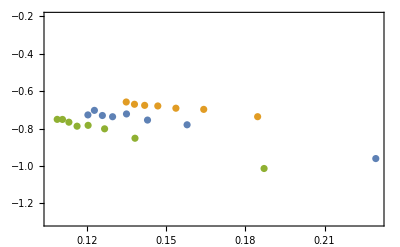

```mathematica
Show[ListPlot[{Reverse@Table[{Nf5α2LoopMid[[i]],Nf5α2LoopΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopBig[[i]],Nf5α2LoopΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1.3,-.2}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

```mathematica
Nf5α2LoopΔEqqbarBig/Nf5α2LoopBig^2
```

{-0.65800.0010,-0.67020.0008,-0.67600.0010,-0.67920.0009,-0.69130.0012,-0.69750.0013,-0.73670.0012,-0.90830.0022}

```mathematica
Nf5α2LoopΔEqqbarSmall/Nf5α2LoopSmall^2
```

{-0.75100.0031,-0.75140.0026,-0.76610.0026,-0.78760.0030,-0.78300.0028,-0.80160.0032,-0.8520.004,-1.0140.007}

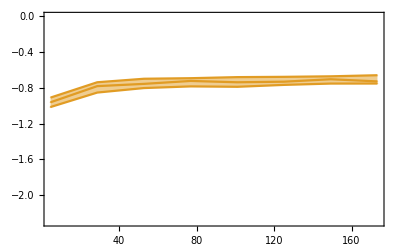

```mathematica
Nf5α2LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.3,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

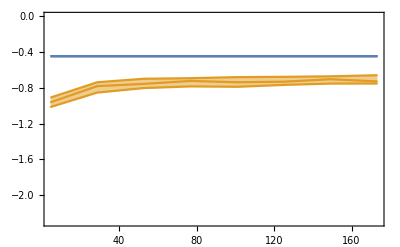

```mathematica
Show[Nf5α2LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot]
```

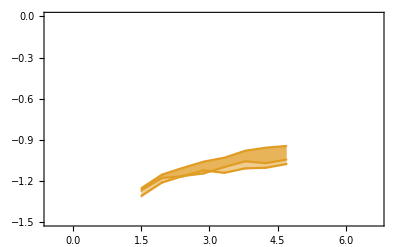

```mathematica
Show[Nf4α2LoopΔEqqbarPlot,PlotRange->{{Mc-2,Mb+2},{-1.5,0}}]
```

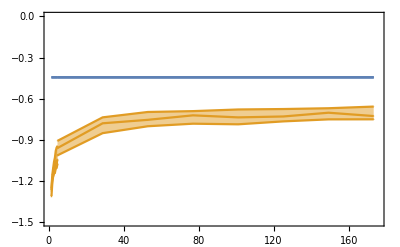

```mathematica
Show[Nf4α2LoopΔEqqbarPlot,Nf5α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{{2Mc-2,Mt+2},{-1.5,0}}]
```

#### NNLO

```mathematica
Nf4α3LoopMid
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopBig]}]
```

{-0.14690.0005,-0.16130.0005,-0.18400.0006,-0.21080.0008,-0.24570.0010,-0.32440.0011,-0.46350.0016,-0.78520.0032}

```mathematica
Nf4α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopMid]}]
```

{-0.08920.0005,-0.09950.0006,-0.10720.0006,-0.11940.0007,-0.13500.0008,-0.15460.0012,-0.19700.0013,-0.25640.0021}

```mathematica
Nf4α3LoopSmall
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Nf4α3LoopStepTab
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf4α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopSmall]}]
```

{-0.06270.0005,-0.06760.0005,-0.07350.0006,-0.07850.0006,-0.08510.0007,-0.09570.0010,-0.11320.0011,-0.13950.0015}

```mathematica
Nf4α3LoopΔEqqbarMid/Nf4α3LoopMid^2
```

{-1.7520.009,-1.8560.011,-1.8830.011,-1.9570.011,-2.0400.012,-2.1140.016,-2.3750.016,-2.6090.022}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf4α3LoopΔEqqbarBig/Nf4α3LoopBig^2
```

{-1.6760.005,-1.7120.006,-1.7970.006,-1.8670.007,-2.0090.008,-2.2420.008,-2.5460.009,-3.0420.012}

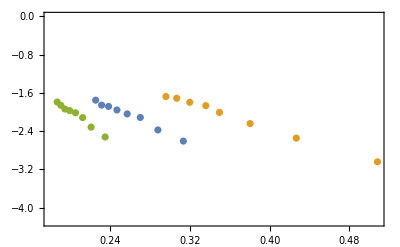

```mathematica
Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],Nf4α3LoopΔEqqbarMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],Nf4α3LoopΔEqqbarBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],Nf4α3LoopΔEqqbarSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

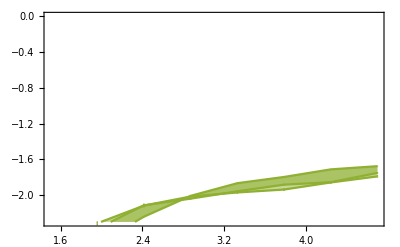

```mathematica
Nf4α3LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqbarMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqbarBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqbarSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{-2.3,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

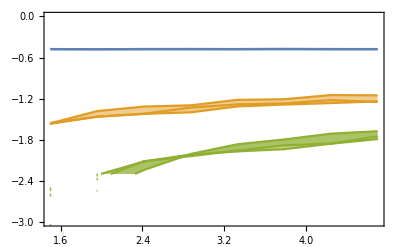

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,Nf4α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,PlotRange->{-3,0}]
```

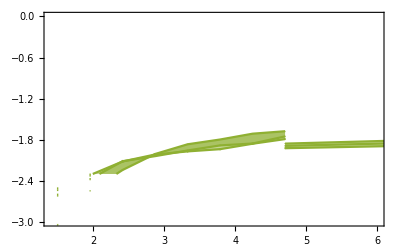

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,Nf5α3LoopΔEqqbarPlot,PlotRange->{{1.4,6},{-3,0}}]
```

```mathematica
Nf5α3LoopMid
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopBig
```

{0.134841,0.137946,0.14178,0.146722,0.153516,0.163936,0.184024,0.296093}

```mathematica
Nf5α3LoopSmall
```

{0.108781,0.110771,0.113203,0.116293,0.120467,0.126701,0.138172,0.187113}

```mathematica
Nf4α3LoopMid
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopBig
```

{0.296093,0.306917,0.319941,0.336039,0.34972,0.380431,0.426678,0.508047}

```mathematica
Nf4α3LoopSmall
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Nf5α3Loopμ
```

{83.4695,73.3338,63.0043,52.434,41.5493,30.2209,18.1659,4.24177}

```mathematica
Nf4α3Loopμ
```

{4.24177,3.9304,3.61282,3.28803,2.95474,2.61112,2.2546,1.88115}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf4α3LoopStepTab
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf5α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopBig]}]
```

{-0.0144080.000018,-0.0154170.000020,-0.0163260.000028,-0.0178510.000032,-0.0202460.000032,-0.023770.00006,-0.032620.00007,-0.12610.0005}

```mathematica
Nf5α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopMid]}]
```

{-0.0127330.000034,-0.013440.00004,-0.014250.00004,-0.015630.00005,-0.017780.00005,-0.019960.00007,-0.026690.00011,-0.07990.0004}

```mathematica
Nf5α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopSmall]}]
```

{-0.011090.00005,-0.011660.00005,-0.012320.00005,-0.013470.00006,-0.014630.00007,-0.017160.00009,-0.022530.00013,-0.05400.0005}

```mathematica
Nf4α3LoopΔEqqbarBig
```

{-0.14690.0005,-0.16130.0005,-0.18400.0006,-0.21080.0008,-0.24570.0010,-0.32440.0011,-0.46350.0016,-0.78520.0032}

```mathematica
Nf4α3LoopΔEqqbarMid
```

{-0.08920.0005,-0.09950.0006,-0.10720.0006,-0.11940.0007,-0.13500.0008,-0.15460.0012,-0.19700.0013,-0.25640.0021}

```mathematica
Nf4α3LoopΔEqqbarSmall
```

{-0.06270.0005,-0.06760.0005,-0.07350.0006,-0.07850.0006,-0.08510.0007,-0.09570.0010,-0.11320.0011,-0.13950.0015}

```mathematica
Nf5α3LoopΔEqqbarMid/Nf5α3LoopMid^2
```

{-0.87860.0023,-0.89090.0025,-0.90000.0028,-0.92920.0027,-0.97620.0028,-0.97780.0035,-1.0730.004,-1.5700.008}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf5α3LoopΔEqqbarBig/Nf5α3LoopBig^2
```

{-0.79240.0010,-0.81020.0010,-0.81220.0014,-0.82920.0015,-0.85910.0014,-0.88430.0022,-0.96340.0022,-1.4380.005}

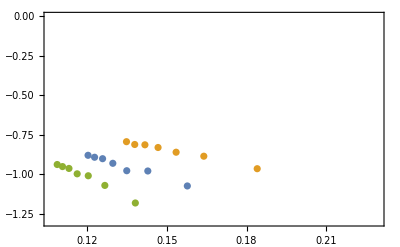

```mathematica
Show[ListPlot[{Reverse@Table[{Nf5α3LoopMid[[i]],Nf5α3LoopΔEqqbarMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopBig[[i]],Nf5α3LoopΔEqqbarBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopSmall[[i]],Nf5α3LoopΔEqqbarSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-1.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

```mathematica
Nf5α3LoopΔEqqbarBig/Nf5α3LoopBig^2
```

{-0.79240.0010,-0.81020.0010,-0.81220.0014,-0.82920.0015,-0.85910.0014,-0.88430.0022,-0.96340.0022,-1.4380.005}

```mathematica
Nf5α3LoopΔEqqbarSmall/Nf5α3LoopSmall^2
```

{-0.9370.004,-0.9500.004,-0.9620.004,-0.9960.005,-1.0080.004,-1.0690.006,-1.1800.007,-1.5420.014}

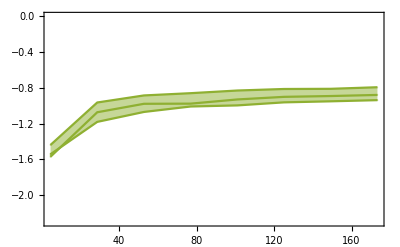

```mathematica
Nf5α3LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqbarMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqbarBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqbarSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.3,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

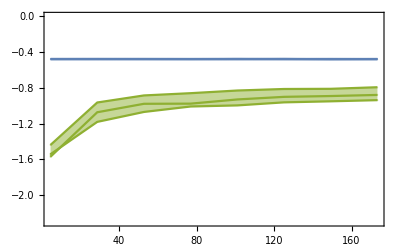

```mathematica
Show[Nf5α3LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot]
```

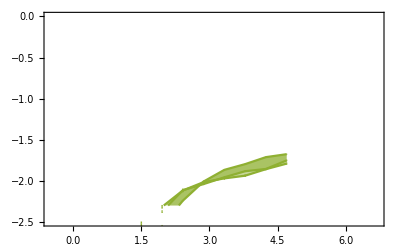

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,PlotRange->{{Mc-2,Mb+2},{-2.5,0}}]
```

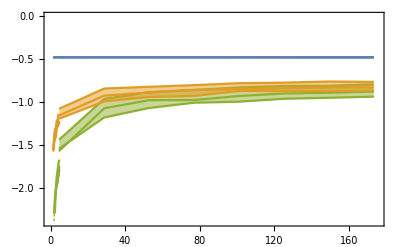

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,Nf5α3LoopΔEqqbarPlot,Nf4α2LoopΔEqqbarPlot,Nf5α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{{0,Mt+2},{-2.4,0}}]
```

### M_QQQ

```mathematica
MbbbLQCD=Around[14.366,Sqrt[.009^2+.020^2]]
```

14.3660.022

```mathematica
MbbbLQCD/3
```

4.7890.007

```mathematica
MbbcLQCD=Around[11.195,Sqrt[.008^2+.020^2]]
```

11.1950.022

```mathematica
MbccLQCD=Around[8.007,Sqrt[.009^2+.020^2]]
```

8.0070.022

```mathematica
McccLQCD=Around[4.796,Sqrt[.008^2+.018^2]]
```

4.7960.020

```mathematica
moops=9.46030;
```

```mathematica
mJPsi=3.096;
```

```mathematica
(* 1S0 *)
```

```mathematica
mJPsi=Around[2.9839,.0005];
```

```mathematica
moops=Around[9.46030,.00026];
```

```mathematica
mJPsi=1/2(Around[2.9839,.0005]+Around[3.096900,.000006])
```

3.040400.00025

```mathematica
moops=1/2(Around[9.46030,.00026]+Around[9.3987,.0020])
```

9.42950.0010

```mathematica
mJPsi=(Around[3.096900,.000006])
```

3.0969006

```mathematica
moops=(Around[9.46030,.00026])
```

9.460300.00026

```mathematica
McccLQCD/mJPsi
```

1.6070.007

```mathematica
mJPsi
```

2.98390.0005

#### LO

```mathematica
Nf4α1LoopMid
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopBig]}]
```

{-0.0344690.000015,-0.0364230.000017,-0.0388590.000019,-0.0420300.000021,-0.0463250.000021,-0.0521460.000027,-0.060860.00004,-0.075120.00004}

```mathematica
Nf4α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopMid]}]
```

{-0.0221080.000012,-0.0231790.000012,-0.0243710.000014,-0.0259390.000013,-0.0278000.000014,-0.0303610.000020,-0.0338180.000020,-0.0389680.000025}

```mathematica
Nf4α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopSmall]}]
```

{-0.0157730.000012,-0.0163390.000010,-0.0169640.000011,-0.0177850.000012,-0.0187330.000013,-0.0199680.000014,-0.0219120.000016,-0.0243740.000020}

```mathematica
ΔEqqqOα2=Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-0.444442622,-0.444446221,-0.444446220,-0.444446218,-0.444444517,-0.444445816,-0.444444214,-0.444445212}

```mathematica
Nf4α1LoopΔEqqqMid/Nf4α1LoopMid^2
```

{-0.475780.00026,-0.476460.00025,-0.475510.00027,-0.476570.00025,-0.475870.00025,-0.477090.00031,-0.477310.00029,-0.476960.00031}

```mathematica
ΔEqqqOα2WD=3/2Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-0.666663832,-0.666669331,-0.666669329,-0.666669328,-0.666666726,-0.666668624,-0.666666321,-0.666667918}

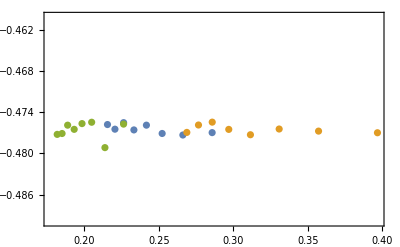

```mathematica
Show[ListPlot[{Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{-.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

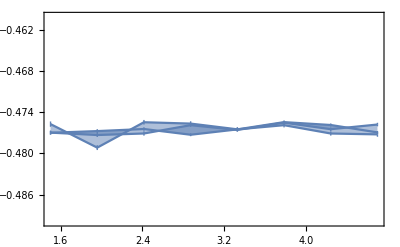

```mathematica
Nf4α1LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{{Mc,Mb},{-.49,-.46}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

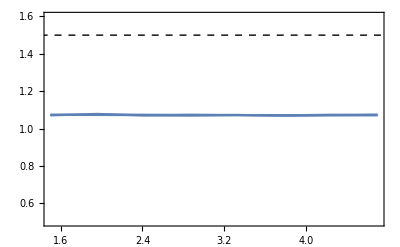

```mathematica
Nf4α1LoopΔEqqbarRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{{Mc,Mb},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

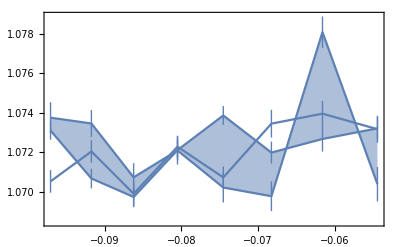

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

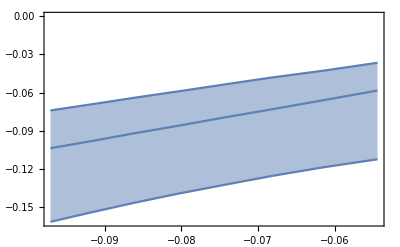

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

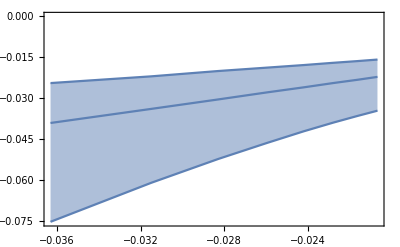

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

```mathematica
Nf5α1LoopMid
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopBig]}]
```

{-0.008480930,-0.008868332,-0.009306031,-0.0099754,-0.0108144,-0.0122175,-0.0151116,-0.0344950.000016}

```mathematica
Nf5α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopMid]}]
```

{-0.006863830,-0.007110530,-0.007480331,-0.007889128,-0.008521534,-0.0094974,-0.0113996,-0.0221100.000013}

```mathematica
Nf5α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopSmall]}]
```

{-0.005652324,-0.005877127,-0.006093926,-0.006411032,-0.006884033,-0.0075654,-0.0089455,-0.0157840.000011}

```mathematica
ΔEqqqOα2=Nf5α1LoopΔEqqbarMid/Nf5α1LoopMid^2
```

{-0.4444487,-0.4444467,-0.4444456,-0.4444476,-0.4444436,-0.4444475,-0.4444464,-0.444442622}

```mathematica
Nf5α1LoopΔEqqqMid/Nf5α1LoopMid^2
```

{-0.477530.00021,-0.476000.00020,-0.478180.00020,-0.476210.00017,-0.477160.00019,-0.477500.00018,-0.476000.00025,-0.475830.00028}

```mathematica
ΔEqqqOα2WD=3/2Nf5α1LoopΔEqqbarMid/Nf5α1LoopMid^2
```

{-0.6666720.000010,-0.6666700.000010,-0.66666710,-0.6666719,-0.6666648,-0.6666708,-0.6666696,-0.666663832}

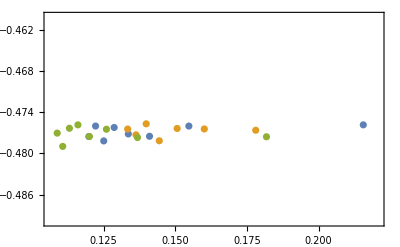

```mathematica
Show[ListPlot[{Table[{Nf5α1LoopMid[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Table[{Nf5α1LoopBig[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Table[{Nf5α1LoopSmall[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{-.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

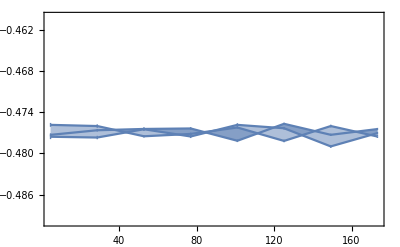

```mathematica
Nf5α1LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{{Mb,Mt},{-.49,-.46}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

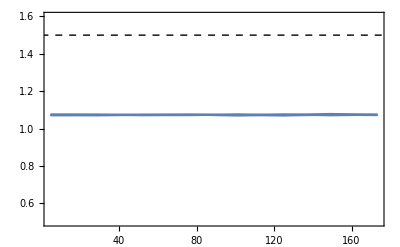

```mathematica
Nf5α1LoopΔEqqbarRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{{Mb,Mt},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

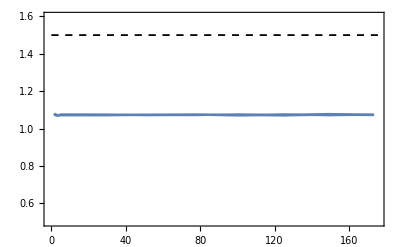

```mathematica
Show[Nf4α1LoopΔEqqbarRatioPlot,Nf5α1LoopΔEqqbarRatioPlot,PlotRange->{{Mc-2,Mt+2},{.5,1.6}}]
```

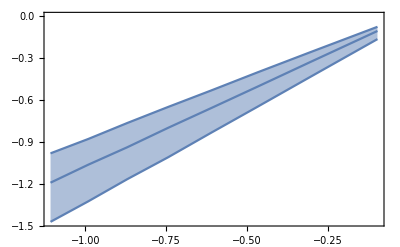

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopMid]}],Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopBig]}],Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

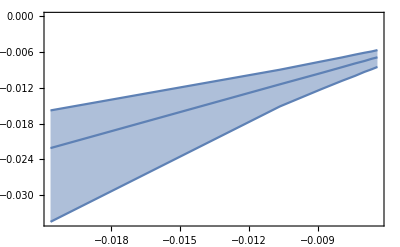

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqMid[[i]]},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqBig[[i]]},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqSmall[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

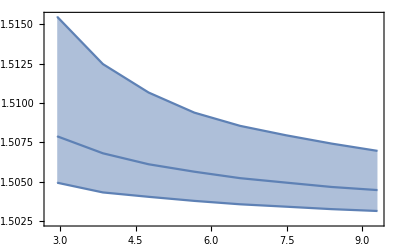

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqMid[[i]])/(2+Nf4α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqBig[[i]])/(2+Nf4α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqSmall[[i]])/(2+Nf4α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

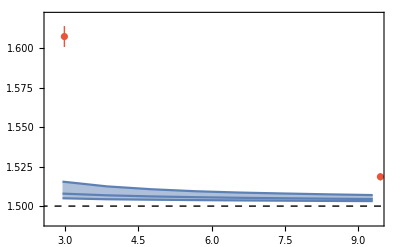

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{1.8Mc,2Mb},{1.49,1.62}},Axes->False]
```

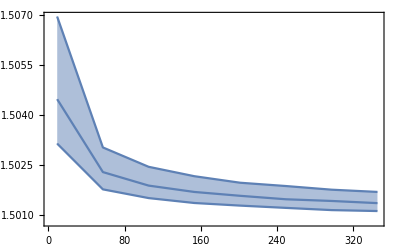

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqMid[[i]])/(2+Nf5α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqBig[[i]])/(2+Nf5α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqSmall[[i]])/(2+Nf5α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

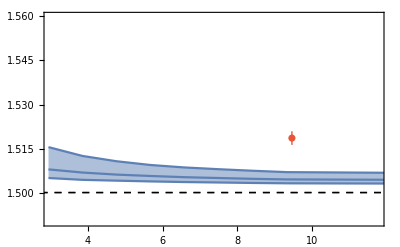

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{2Mc,2.5Mb},{1.49,1.56}},Axes->False]
```

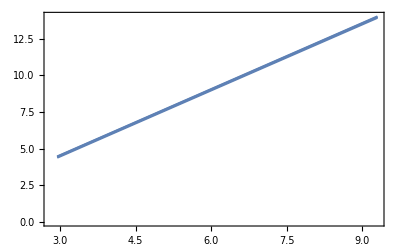

```mathematica
Nf4α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqqMid[[i]]Nf4α1LoopmQ[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopmQ[[i]]Nf4α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopmQ[[i]]Nf4α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

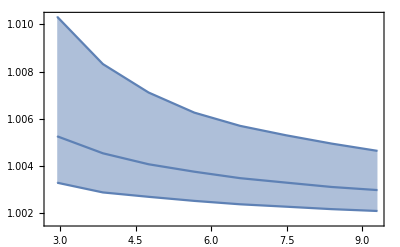

```mathematica
Nf4α1LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqMid[[i]])/(2+Nf4α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqBig[[i]])/(2+Nf4α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqSmall[[i]])/(2+Nf4α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

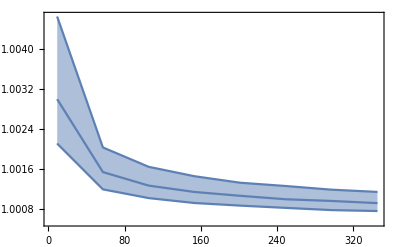

```mathematica
Nf5α1LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqMid[[i]])/(2+Nf5α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqBig[[i]])/(2+Nf5α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqSmall[[i]])/(2+Nf5α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

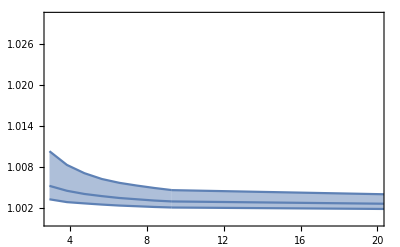

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,PlotRange->{{3,20},{1,1.03}}]
```

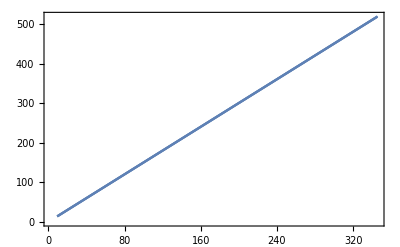

```mathematica
Nf5α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqqMid[[i]]Nf5α1LoopmQ[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopmQ[[i]]Nf5α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopmQ[[i]]Nf5α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

#### NLO

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopBig]}]
```

{-0.108850.00035,-0.11740.0004,-0.13550.0004,-0.15220.0007,-0.18530.0006,-0.21490.0010,-0.29400.0013,-0.49790.0019}

```mathematica
Nf4α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopMid]}]
```

{-0.065740.00029,-0.067870.00034,-0.07500.0004,-0.08160.0004,-0.09210.0005,-0.10930.0006,-0.12870.0007,-0.16390.0011}

```mathematica
Nf4α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopSmall]}]
```

{-0.043410.00029,-0.045990.00032,-0.048830.00032,-0.05240.0004,-0.05910.0004,-0.06430.0005,-0.07310.0006,-0.08890.0008}

```mathematica
ΔEqqqOα2=Nf4α2LoopΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.0450.005,-1.0720.006,-1.0580.006,-1.1000.007,-1.1460.007,-1.1650.007,-1.2120.008,-1.3110.009}

```mathematica
Nf4α2LoopΔEqqqMid/Nf4α2LoopMid^2
```

{-1.2490.006,-1.2210.006,-1.2690.006,-1.2840.007,-1.3310.008,-1.4210.008,-1.4640.008,-1.5570.011}

```mathematica
ΔEqqqOα2WD=3/2Nf4α2LoopΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.5670.008,-1.6070.008,-1.5870.008,-1.6500.010,-1.7190.011,-1.7480.010,-1.8190.012,-1.9670.013}

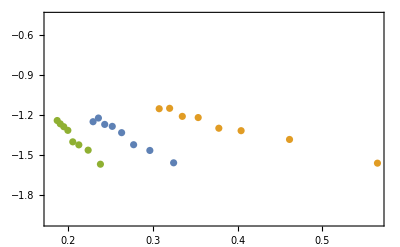

```mathematica
Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

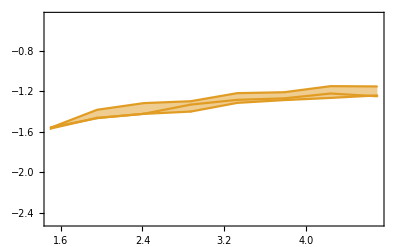

```mathematica
Nf4α2LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

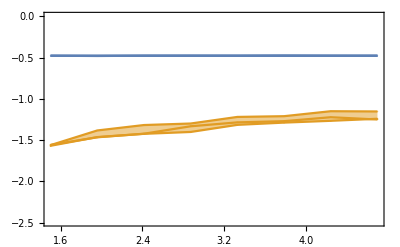

```mathematica
Show[Nf4α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,PlotRange->{-2.49,0}]
```

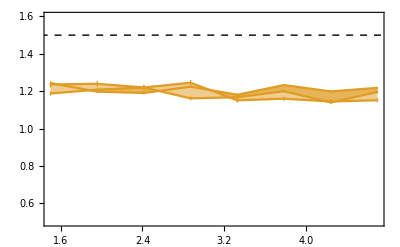

```mathematica
Nf4α2LoopΔEqqbarRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

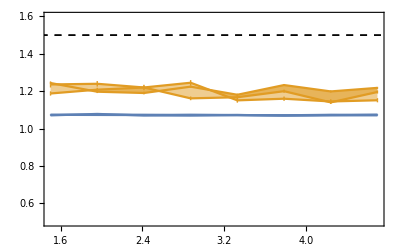

```mathematica
Show[Nf4α2LoopΔEqqbarRatioPlot,Nf4α1LoopΔEqqbarRatioPlot]
```

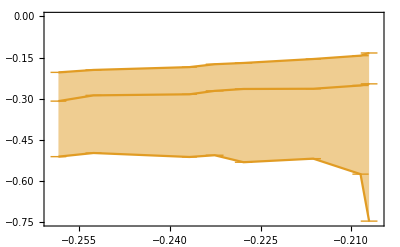

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

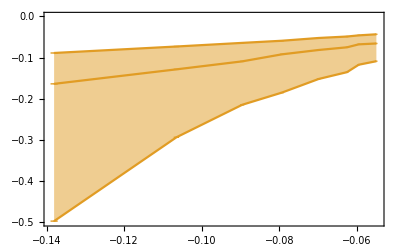

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

```mathematica
Show[Nf4α2LoopΔEqqbarVsPlot,Nf4α1LoopΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nf5α2LoopMid
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopBig]}]
```

{-0.0139050.000016,-0.0144860.000024,-0.0155700.000020,-0.0168140.000024,-0.0189610.000030,-0.0221730.000034,-0.028720.00005,-0.101830.00035}

```mathematica
Nf5α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopMid]}]
```

{-0.0120190.000026,-0.0125310.000028,-0.0132940.000032,-0.014280.00004,-0.015630.00004,-0.018170.00006,-0.023080.00007,-0.060830.00032}

```mathematica
Nf5α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopSmall]}]
```

{-0.0102520.000035,-0.010680.00004,-0.011170.00004,-0.011780.00004,-0.013470.00006,-0.015100.00006,-0.018970.00008,-0.041780.00026}

```mathematica
ΔEqqqOα2=Nf5α2LoopΔEqqbarMid/Nf5α2LoopMid^2
```

{-0.72720.0017,-0.70280.0018,-0.73030.0017,-0.73690.0019,-0.72190.0021,-0.75480.0021,-0.78000.0031,-0.9610.005}

```mathematica
Nf5α2LoopΔEqqqMid/Nf5α2LoopMid^2
```

{-0.82940.0018,-0.83040.0018,-0.83920.0020,-0.84860.0023,-0.85790.0024,-0.88890.0028,-0.92500.0026,-1.1560.006}

```mathematica
ΔEqqqOα2WD=3/2Nf5α2LoopΔEqqbarMid/Nf5α2LoopMid^2
```

{-1.09080.0025,-1.05420.0026,-1.09540.0026,-1.10540.0029,-1.08290.0031,-1.13220.0032,-1.1700.005,-1.4410.007}

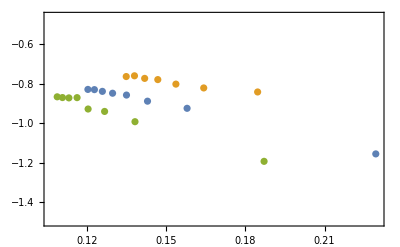

```mathematica
Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Table[{Nf5α2LoopBig[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1.5,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

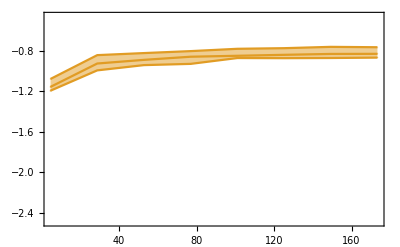

```mathematica
Nf5α2LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

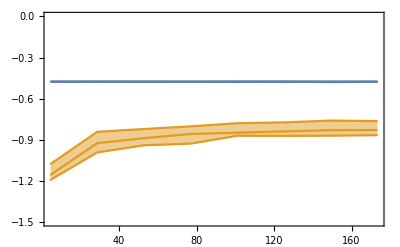

```mathematica
Show[Nf5α2LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{-1.5,0},Axes->False]
```

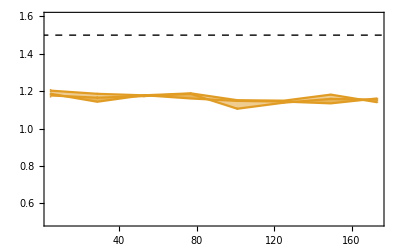

```mathematica
Nf5α2LoopΔEqqbarRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

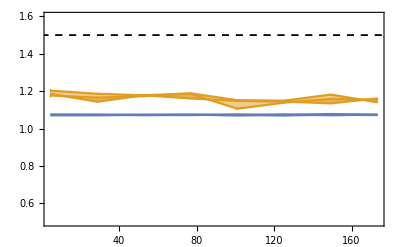

```mathematica
Show[Nf5α2LoopΔEqqbarRatioPlot,Nf5α1LoopΔEqqbarRatioPlot]
```

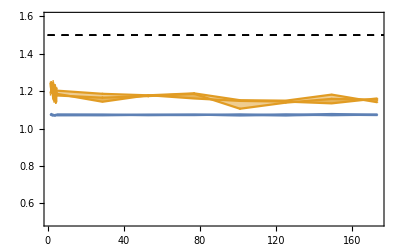

```mathematica
Show[Nf4α2LoopΔEqqbarRatioPlot,Nf5α2LoopΔEqqbarRatioPlot,Nf4α1LoopΔEqqbarRatioPlot,Nf5α1LoopΔEqqbarRatioPlot,PlotRange->{{Mc,Mt},{.5,1.6}}]
```

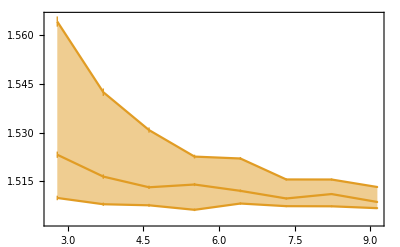

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqMid[[i]])/(2+Nf4α2LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqBig[[i]])/(2+Nf4α2LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqSmall[[i]])/(2+Nf4α2LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
mJPsi
```

3.0969006

```mathematica
McccLQCD/mJPsi
```

1.5490.006

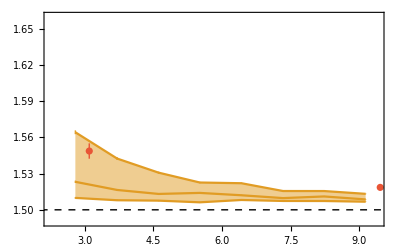

```mathematica
Show[Nf4α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi[[1]],McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{1.5Mc,2Mb},{1.49,1.66}},Axes->False]
```

```mathematica
Table[Series[(3+Nf5α1LoopΔEqqqBig[[ii]]  αα^2/Nf5α1LoopMid[[ii]]^2)/(2+Nf5α1LoopΔEqqbarBig[[ii]] αα^2/Nf5α1LoopMid[[ii]]^2),{αα,0,2}],{ii,1,8}]
```

{3/2+(0.117790.00011) αα^2+O[αα]^3,3/2+(0.117780.00011) αα^2+O[αα]^3,3/2+(0.119430.00010) αα^2+O[αα]^3,3/2+(0.118690.00012) αα^2+O[αα]^3,3/2+(0.120950.00012) αα^2+O[αα]^3,3/2+(0.122630.00013) αα^2+O[αα]^3,3/2+(0.125800.00013) αα^2+O[αα]^3,3/2+(0.147280.00017) αα^2+O[αα]^3}

```mathematica
Table[Series[(3+Nf5α2LoopΔEqqqBig[[ii]]  αα^2/Nf5α2LoopMid[[ii]]^2)/(2+Nf5α2LoopΔEqqbarBig[[ii]] αα^2/Nf5α2LoopMid[[ii]]^2),{αα,0,2}],{ii,1,8}]
```

{3/2+(0.13990.0011) αα^2+O[αα]^3,3/2+(0.15460.0011) αα^2+O[αα]^3,3/2+(0.15280.0011) αα^2+O[αα]^3,3/2+(0.15330.0011) αα^2+O[αα]^3,3/2+(0.15190.0014) αα^2+O[αα]^3,3/2+(0.14810.0015) αα^2+O[αα]^3,3/2+(0.17960.0016) αα^2+O[αα]^3,3/2+(0.2560.004) αα^2+O[αα]^3}

```mathematica
.12 .4^2
```

0.0192

```mathematica
.12 .2^2
```

0.0048

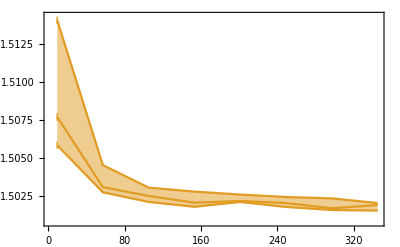

```mathematica
Nf5α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqBig[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqSmall[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

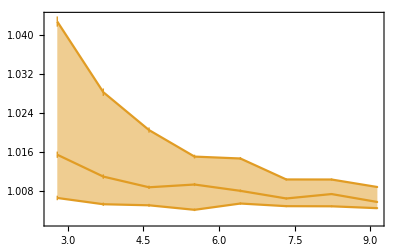

```mathematica
Nf4α2LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

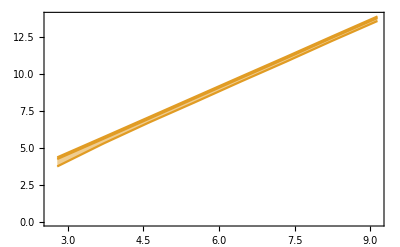

```mathematica
Nf4α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmQ[[i]]Nf4α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmQ[[i]]Nf4α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

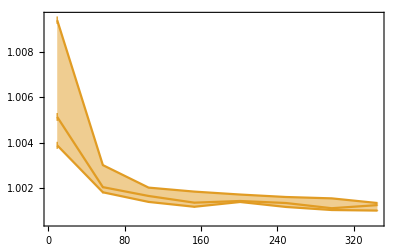

```mathematica
Nf5α2LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqBig[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqSmall[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

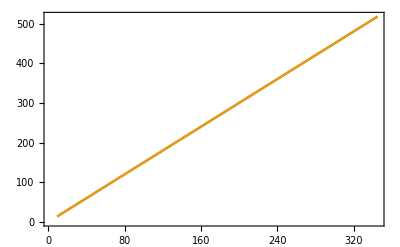

```mathematica
Nf5α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmQ[[i]]Nf5α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmQ[[i]]Nf5α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

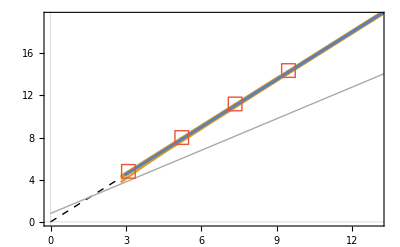

```mathematica
scale=13;Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Graphics[{Lighter[Gray],Line[{{0,.800},{1000,.800+1000}}]}],Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

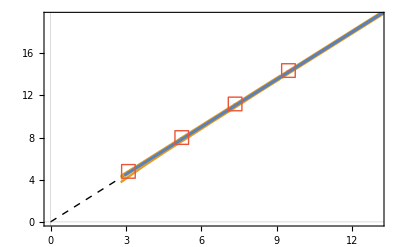

```mathematica
scale=13;Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

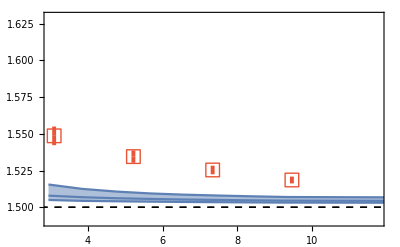

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.63}},Axes->False]
```

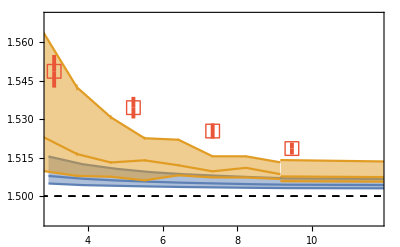

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.57}},Axes->False]
```

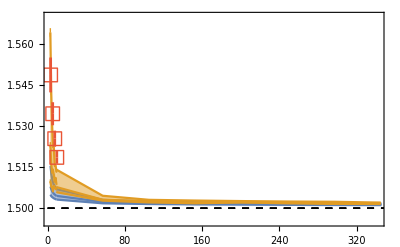

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,1.97Mt},{1.495,1.57}},Axes->False]
```

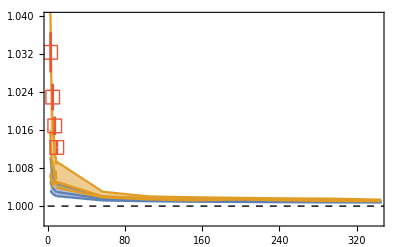

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

#### NNLO

```mathematica
Nf4α3LoopMid
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopBig]}]
```

{-0.18390.0006,-0.20710.0007,-0.23580.0008,-0.26930.0010,-0.31020.0012,-0.41260.0015,-0.59450.0023,-1.0300.004}

```mathematica
Nf4α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopMid]}]
```

{-0.10690.0006,-0.11790.0006,-0.13230.0008,-0.14450.0009,-0.17040.0010,-0.19660.0012,-0.24920.0016,-0.33540.0020}

```mathematica
Nf4α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopSmall]}]
```

{-0.07760.0006,-0.08350.0006,-0.09230.0006,-0.09850.0008,-0.10760.0008,-0.12370.0010,-0.14140.0013,-0.18020.0016}

```mathematica
ΔEqqqOα2=Nf4α3LoopΔEqqbarMid/Nf4α3LoopMid^2
```

{-1.7520.009,-1.8560.011,-1.8830.011,-1.9570.011,-2.0400.012,-2.1140.016,-2.3750.016,-2.6090.022}

```mathematica
Nf4α3LoopΔEqqqMid/Nf4α3LoopMid^2
```

{-2.1000.012,-2.1990.012,-2.3240.014,-2.3690.014,-2.5740.015,-2.6890.017,-3.0040.019,-3.4120.020}

```mathematica
ΔEqqqOα2WD=3/2Nf4α3LoopΔEqqbarMid/Nf4α3LoopMid^2
```

{-2.6280.014,-2.7840.016,-2.8250.016,-2.9360.017,-3.0590.019,-3.1710.025,-3.5630.024,-3.9130.033}

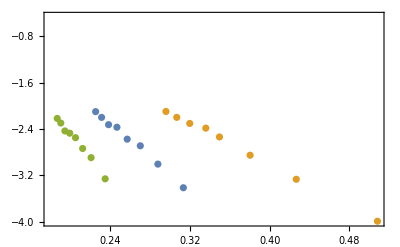

```mathematica
Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-4,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

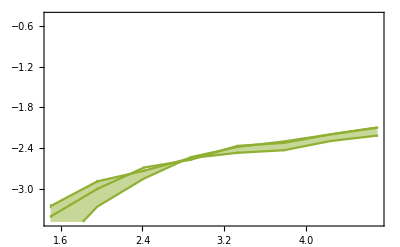

```mathematica
Nf4α3LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{-3.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

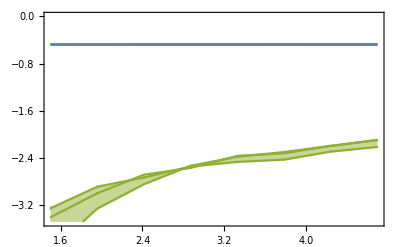

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,PlotRange->{-3.49,0}]
```

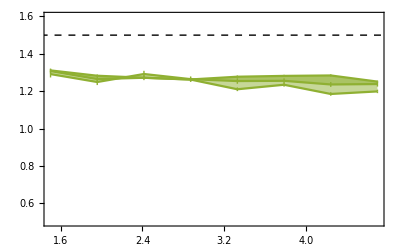

```mathematica
Nf4α3LoopΔEqqbarRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

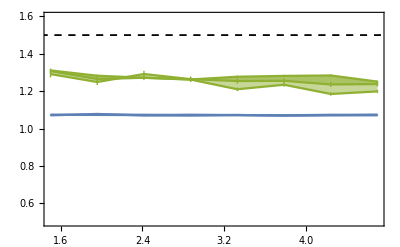

```mathematica
Show[Nf4α3LoopΔEqqbarRatioPlot,Nf4α1LoopΔEqqbarRatioPlot]
```

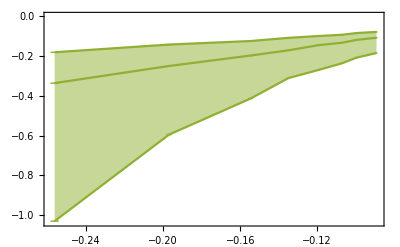

```mathematica
Nf4α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

```mathematica
Show[Nf4α3LoopΔEqqbarVsPlot,Nf4α1LoopΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nf5α3LoopMid
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopBig]}]
```

{-0.0169610.000026,-0.0181800.000030,-0.0196350.000034,-0.021280.00004,-0.024090.00005,-0.029320.00005,-0.039860.00009,-0.16280.0005}

```mathematica
Nf5α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopMid]}]
```

{-0.014850.00005,-0.015970.00005,-0.016940.00005,-0.018200.00007,-0.020650.00007,-0.024470.00008,-0.032220.00011,-0.09620.0004}

```mathematica
Nf5α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopSmall]}]
```

{-0.013390.00005,-0.014110.00006,-0.014670.00006,-0.016160.00007,-0.017820.00007,-0.020840.00009,-0.027110.00012,-0.06740.0005}

```mathematica
ΔEqqqOα2=Nf5α3LoopΔEqqbarMid/Nf5α3LoopMid^2
```

{-0.87860.0023,-0.89090.0025,-0.90000.0028,-0.92920.0027,-0.97620.0028,-0.97780.0035,-1.0730.004,-1.5700.008}

```mathematica
Nf5α3LoopΔEqqqMid/Nf5α3LoopMid^2
```

{-1.02440.0033,-1.05820.0032,-1.06980.0031,-1.0820.004,-1.1340.004,-1.1990.004,-1.2950.004,-1.8900.008}

```mathematica
ΔEqqqOα2WD=3/2Nf5α3LoopΔEqqbarMid/Nf5α3LoopMid^2
```

{-1.31790.0035,-1.3360.004,-1.3500.004,-1.3940.004,-1.4640.004,-1.4670.005,-1.6090.007,-2.3550.012}

```mathematica
Nf5α3LoopΔEqqqMid
```

{-0.014850.00005,-0.015970.00005,-0.016940.00005,-0.018200.00007,-0.020650.00007,-0.024470.00008,-0.032220.00011,-0.09620.0004}

```mathematica
Nf4α3LoopΔEqqqMid
```

{-0.10690.0006,-0.11790.0006,-0.13230.0008,-0.14450.0009,-0.17040.0010,-0.19660.0012,-0.24920.0016,-0.33540.0020}

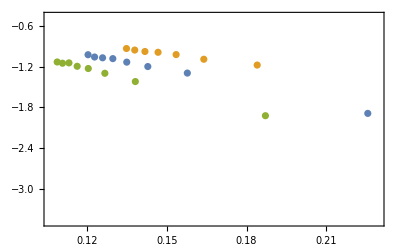

```mathematica
Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

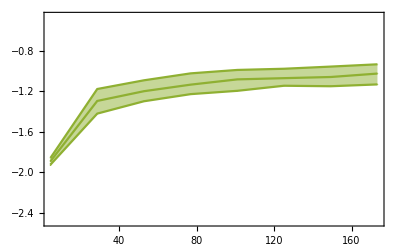

```mathematica
Nf5α3LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

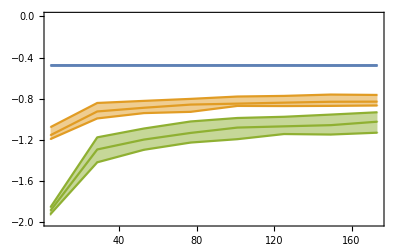

```mathematica
Show[Nf5α3LoopΔEqqbarPlot,Nf5α2LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{-2.,0},Axes->False]
```

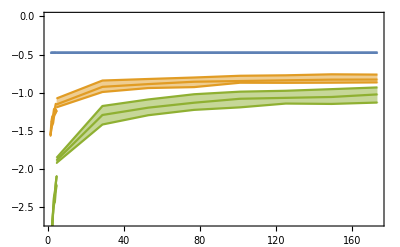

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,Nf5α3LoopΔEqqbarPlot,Nf4α2LoopΔEqqbarPlot,Nf5α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{-2.7,0},Axes->False]
```

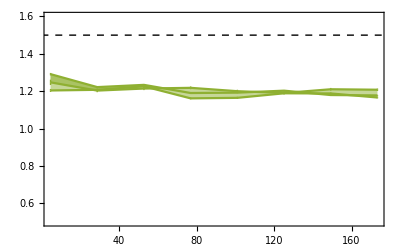

```mathematica
Nf5α3LoopΔEqqbarRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{{Mb,Mt},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

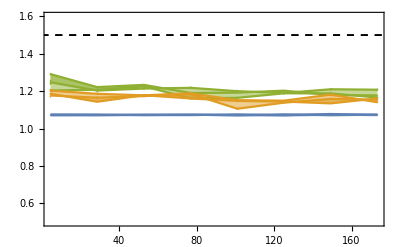

```mathematica
Show[Nf5α3LoopΔEqqbarRatioPlot,Nf5α2LoopΔEqqbarRatioPlot,Nf5α1LoopΔEqqbarRatioPlot]
```

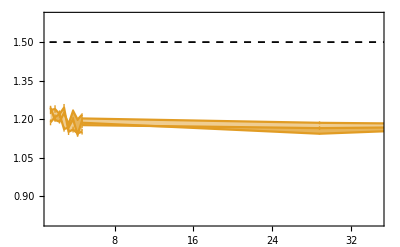

```mathematica
Show[Nf4α2LoopΔEqqbarRatioPlot,Nf5α2LoopΔEqqbarRatioPlot,PlotRange->{{Mc,.2Mt},{.8,1.6}}]
```

```mathematica
Nf5α2LoopΔEqqbarRatioPlot
```

-Graphics-

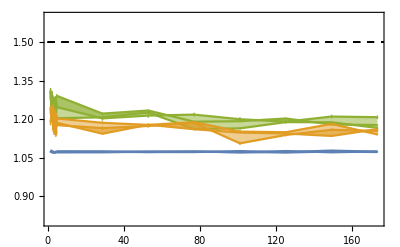

```mathematica
Show[Nf4α3LoopΔEqqbarRatioPlot,Nf5α3LoopΔEqqbarRatioPlot,Nf4α2LoopΔEqqbarRatioPlot,Nf5α2LoopΔEqqbarRatioPlot,Nf4α1LoopΔEqqbarRatioPlot,Nf5α1LoopΔEqqbarRatioPlot,PlotRange->{{Mc,Mt},{.8,1.6}}]
```

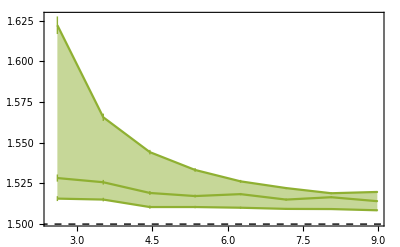

```mathematica
Nf4α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqBig[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarBig[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqSmall[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarSmall[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

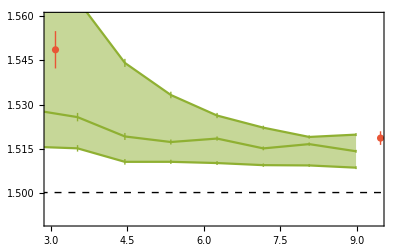

```mathematica
Show[Nf4α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{2Mc,2Mb},{1.49,1.56}},Axes->False]
```

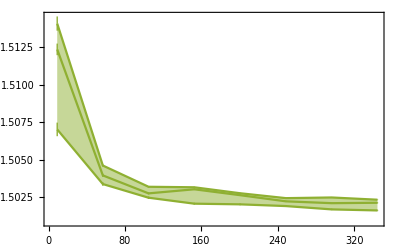

```mathematica
Nf5α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqBig[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarBig[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqSmall[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarSmall[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

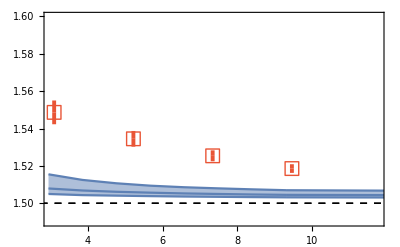

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.60}},Axes->False]
```

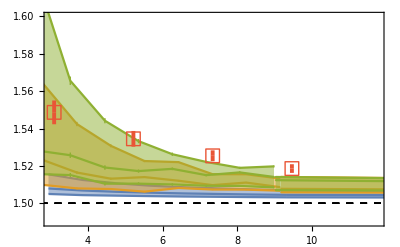

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.60}},Axes->False]
```

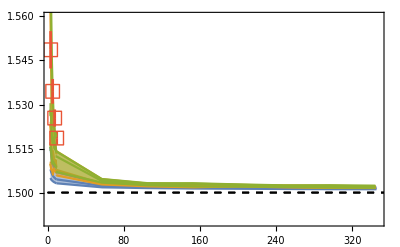

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2Mt},{1.49,1.56}},Axes->False]
```

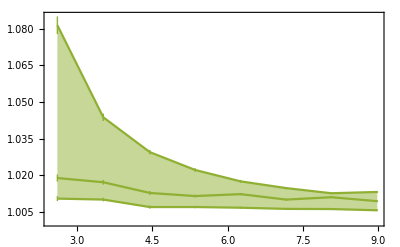

```mathematica
Nf4α3LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqBig[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarBig[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqSmall[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarSmall[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

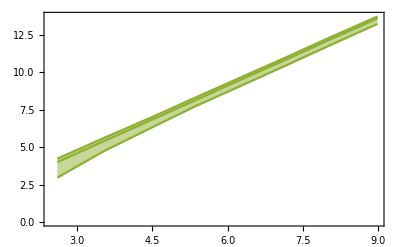

```mathematica
Nf4α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopmQ[[i]]Nf4α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopmQ[[i]]Nf4α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

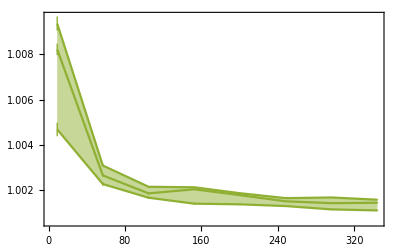

```mathematica
Nf5α3LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqBig[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarBig[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqSmall[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarSmall[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

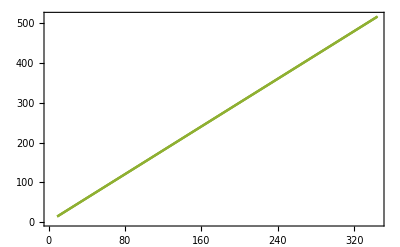

```mathematica
Nf5α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopmQ[[i]]Nf5α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopmQ[[i]]Nf5α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

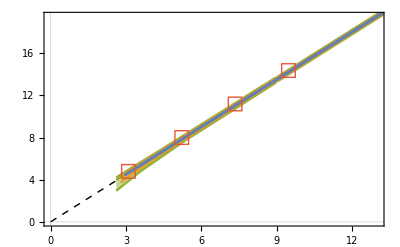

```mathematica
scale=13;Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α3LoopΔEqqbarVsPlotNoRatio,Nf5α3LoopΔEqqbarVsPlotNoRatio,Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

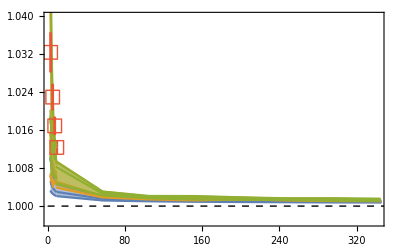

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

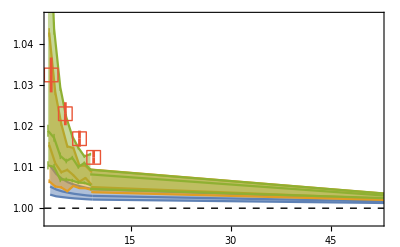

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.3Mt},{2/3 1.495,2/3 1.57}},Axes->False]
```

## dQCD

### α

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>3
αs[3]
```

0.16074

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.07884

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211767

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231173

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0650813

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.183929

0.193995

0.198324

0.16676

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.08325

6.48864

23.0481

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.1942

20.3311

72.2174

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

818.54

749.827

2663.44

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767}

{0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173}

{0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222913,0.282356,0.423534,0.847069,4.23534,21.1767,211.767}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.24334,0.308231,0.462347,0.924693,4.62347,23.1173,231.173}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685066,0.0867751,0.130163,0.260325,1.30163,6.50813,65.0813}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{181472.,10.4543,0.237118,0.267327,0.14756,0.101565,0.0707307}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{6214.1,9.42661,0.748873,0.304487,0.149909,0.102174,0.0709126}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{25.3853,2.69684,0.712084,0.307309,0.14697,0.100342,0.0699798}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{11.1359,1.98552,0.824065,0.412033,0.190671,0.124034,0.0826895}

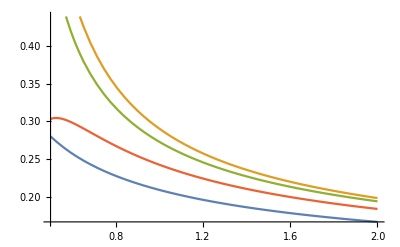

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

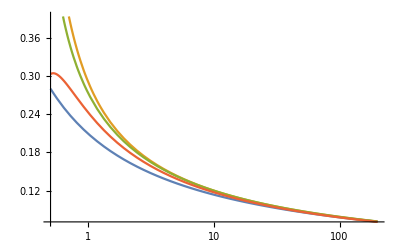

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nf0α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,{2Λ1LoopNf0,4Λ1LoopNf0,8Λ1LoopNf0,16Λ1LoopNf0,32Λ1LoopNf0,64Λ1LoopNf0,128Λ1LoopNf0,256Λ1LoopNf0}}]
```

{0.233099,0.352229,0.55501,0.904154,1.51254,2.5848,4.49434,7.92665}

```mathematica
Nf0α1LoopMid=Table[αs1Loop[Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopMid=Table[αs1Loop[Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopStepTab=Round[2/(.2 Nf0α1LoopMid^2)]
```

{50,87,141,212,303,415,550,707}

```mathematica
Nf0α1LoopBig=Table[αs1Loop[1/2Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.980294,0.573782,0.393875,0.294703,0.23288,0.191125,0.161274,0.139005}

```mathematica
Nf0α1LoopSmall=Table[αs1Loop[2Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.290099,0.239819,0.201375,0.171814,0.148786,0.130562,0.115907,0.103939}

```mathematica
Length[DeleteDuplicates[Join[Nf0α1LoopMid,Nf0α1LoopBig,Nf0α1LoopSmall]]]
```

24

```mathematica
Nf0α1LoopmQ=Table[mQ,{mQ,{2Λ1LoopNf0,4Λ1LoopNf0,8Λ1LoopNf0,16Λ1LoopNf0,32Λ1LoopNf0,64Λ1LoopNf0,128Λ1LoopNf0,256Λ1LoopNf0}}]
```

{0.130163,0.260325,0.52065,1.0413,2.0826,4.1652,8.3304,16.6608}

```mathematica
Nf0α1LoopmQoLam=Table[mQ/Λ1LoopNf0,{mQ,{2Λ1LoopNf0,4Λ1LoopNf0,8Λ1LoopNf0,16Λ1LoopNf0,32Λ1LoopNf0,64Λ1LoopNf0,128Λ1LoopNf0,256Λ1LoopNf0}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nf0α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.713559,1.04247,1.61795,2.62765,4.41104,7.58823,13.2991,23.6498}

```mathematica
Nf0mQTab=Table[mQ,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.462347,0.924693,1.84939,3.69877,7.39755,14.7951,29.5902,59.1804}

```mathematica
Nf0α2Loopμ/Nf0mQTab
```

{1.54334,1.12737,0.874856,0.710411,0.596284,0.512888,0.449442,0.399622}

```mathematica
2Nf0α2Loopμ/Nf0mQTab
```

{3.08668,2.25474,1.74971,1.42082,1.19257,1.02578,0.898884,0.799244}

```mathematica
1/2Nf0α2Loopμ/Nf0mQTab
```

{0.771671,0.563686,0.437428,0.355206,0.298142,0.256444,0.224721,0.199811}

```mathematica
Nf0α2LoopMid=Table[αs2Loop[Nf0α2Loopμ[[k]]],{k,1,Length[Nf0α2Loopμ]}]
```

{0.385835,0.281843,0.218714,0.177603,0.149071,0.128222,0.112361,0.0999055}

```mathematica
Nf0α2LoopStepTab=Round[2/(.2 Nf0α2LoopMid^2)]
```

{67,126,209,317,450,608,792,1002}

```mathematica
Nf0α2LoopBig=Table[αs2Loop[1/2Nf0α2Loopμ[[k]]],{k,1,Length[Nf0α2Loopμ]}]
```

{1.41809,0.574986,0.342793,0.244109,0.190293,0.156271,0.132692,0.115324}

```mathematica
Nf0α2LoopSmall=Table[αs2Loop[2Nf0α2Loopμ[[k]]],{k,1,Length[Nf0α2Loopμ]}]
```

{0.233246,0.194817,0.164772,0.141566,0.123504,0.109218,0.0977139,0.0882898}

```mathematica
Length[DeleteDuplicates[Join[Nf0α2LoopMid,Nf0α2LoopBig,Nf0α2LoopSmall]]]
```

24

```mathematica
Nf0α2LoopmQ=Table[mQ,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.462347,0.924693,1.84939,3.69877,7.39755,14.7951,29.5902,59.1804}

```mathematica
Nf0α2LoopmQoLam=Table[mQ/Λ2LoopNf0,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NNLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nf0α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,{2Λ3LoopNf0,4Λ3LoopNf0,8Λ3LoopNf0,16Λ3LoopNf0,32Λ3LoopNf0,64Λ3LoopNf0,128Λ3LoopNf0,256Λ3LoopNf0}}]
```

{0.647079,0.952661,1.4922,2.43729,4.10239,7.06299,12.3764,21.9945}

```mathematica
Nf0mQTab=Table[mQ,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.462347,0.924693,1.84939,3.69877,7.39755,14.7951,29.5902,59.1804}

```mathematica
Nf0α3Loopμ/Nf0mQTab
```

{1.39955,1.03025,0.806862,0.658947,0.55456,0.477388,0.41826,0.371652}

```mathematica
2Nf0α3Loopμ/Nf0mQTab
```

{2.79911,2.06049,1.61372,1.31789,1.10912,0.954775,0.83652,0.743304}

```mathematica
1/2Nf0α3Loopμ/Nf0mQTab
```

{0.699776,0.515123,0.403431,0.329473,0.27728,0.238694,0.20913,0.185826}

```mathematica
Nf0α3LoopMid=Table[αs1Loop[Nf0α3Loopμ[[k]]],{k,1,Length[Nf0α3Loopμ]}]
```

{0.24869,0.212846,0.182354,0.157659,0.137848,0.121869,0.108843,0.098095}

```mathematica
Nf0α3LoopStepTab=Round[2/(.2 Nf0α3LoopMid^2)]
```

{162,221,301,402,526,673,844,1039}

```mathematica
Nf0α3LoopBig=Table[αs3Loop[1/2Nf0α3Loopμ[[k]]],{k,1,Length[Nf0α3Loopμ]}]
```

{2.50606,0.577254,0.335683,0.243572,0.192049,0.158505,0.134819,0.117188}

```mathematica
Nf0α3LoopSmall=Table[αs3Loop[2Nf0α3Loopμ[[k]]],{k,1,Length[Nf0α3Loopμ]}]
```

{0.236064,0.197851,0.167472,0.143912,0.125519,0.110934,0.0991709,0.0895271}

```mathematica
Length[DeleteDuplicates[Join[Nf0α3LoopMid,Nf0α3LoopBig,Nf0α3LoopSmall]]]
```

24

```mathematica
Nf0α3LoopmQ=Table[mQ,{mQ,{2Λ3LoopNf0,4Λ3LoopNf0,8Λ3LoopNf0,16Λ3LoopNf0,32Λ3LoopNf0,64Λ3LoopNf0,128Λ3LoopNf0,256Λ3LoopNf0}}]
```

{0.423534,0.847069,1.69414,3.38828,6.77655,13.5531,27.1062,54.2124}

```mathematica
Nf0α3LoopmQoLam=Table[mQ/Λ3LoopNf0,{mQ,{2Λ3LoopNf0,4Λ3LoopNf0,8Λ3LoopNf0,16Λ3LoopNf0,32Λ3LoopNf0,64Λ3LoopNf0,128Λ3LoopNf0,256Λ3LoopNf0}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

### M_QQbar

```mathematica
datadir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
NWalkers=200;
```

```mathematica
<<MaTeX`
```

#### LO

```mathematica
Nf0α1LoopMid
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopBig]}]
```

{-0.4271005910,-0.1463225710,-0.0689500110,-0.0385999410,-0.0241036010,-0.0162350110,-0.0115596910,-0.0085877310}

```mathematica
Nf0α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopMid]}]
```

{-0.0890855310,-0.0508529610,-0.0315649710,-0.0209425310,-0.0146521310,-0.0106974910,-0.0080853710,-0.0062876410}

```mathematica
Nf0α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopSmall]}]
```

{-0.0374033010,-0.0255614010,-0.0180230610,-0.0131200210,-0.0098387910,-0.0075761910,-0.0059708610,-0.0048014710}

```mathematica
Nf0α1LoopΔEqqbarMid/Nf0α1LoopMid^2
```

{-0.44444405,-0.44444529,-0.444443514,-0.444443221,-0.444445930,-0.4444474,-0.4444465,-0.4444487}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

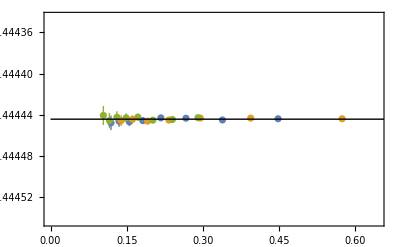

```mathematica
Show[ListPlot[{Table[{Nf0α1LoopMid[[i]],Nf0α1LoopΔEqqbarMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopBig[[i]],Nf0α1LoopΔEqqbarBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopSmall[[i]],Nf0α1LoopΔEqqbarSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

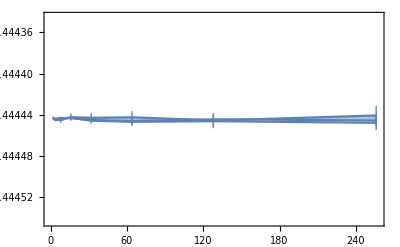

```mathematica
Nf0α1LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqbarMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqbarBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqbarSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{{0,257},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

#### NLO

```mathematica
Nf0α2LoopMid
```

{0.385835,0.281843,0.218714,0.177603,0.149071,0.128222,0.112361,0.0999055}

```mathematica
Nf0α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopBig]}]
```

{-4.1146009110,-0.50070.0016,-0.13780.0005,-0.059010.00022,-0.032460.00011,-0.020030.00006,-0.013370.00004,-0.0095770.000025}

```mathematica
Nf0α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopMid]}]
```

{-0.27990.0030,-0.11780.0012,-0.05810.0005,-0.033190.00024,-0.020750.00013,-0.014270.00007,-0.010220.00004,-0.0076470.000030}

```mathematica
Nf0α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopSmall]}]
```

{-0.09150.0017,-0.05350.0008,-0.03380.0004,-0.021280.00022,-0.015480.00013,-0.010840.00008,-0.008290.00005,-0.006300.00004}

```mathematica
Nf0α2LoopΔEqqbarMid/Nf0α2LoopMid^2
```

{-1.8800.020,-1.4830.015,-1.2150.011,-1.0520.008,-0.9340.006,-0.8680.004,-0.80970.0033,-0.76610.0030}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf0α2LoopΔEqqbarBig/Nf0α2LoopBig^2
```

{-2.046054615,-1.5140.005,-1.1730.004,-0.9900.004,-0.89630.0030,-0.82010.0026,-0.75910.0021,-0.72010.0018}

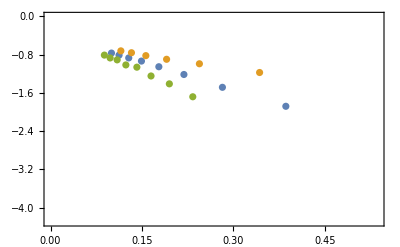

```mathematica
Show[ListPlot[{Table[{Nf0α2LoopMid[[i]],Nf0α2LoopΔEqqbarMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopBig[[i]],Nf0α2LoopΔEqqbarBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopSmall[[i]],Nf0α2LoopΔEqqbarSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

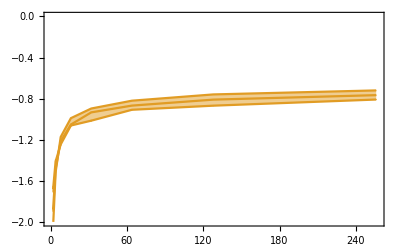

```mathematica
Nf0α2LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqbarMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqbarBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqbarSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{-2.,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

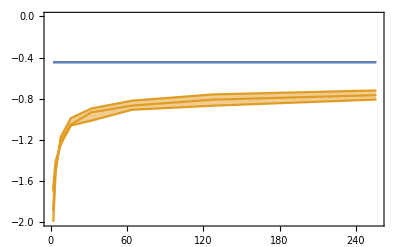

```mathematica
Show[Nf0α2LoopΔEqqbarPlot,Nf0α1LoopΔEqqbarPlot,Axes->False]
```

#### NNLO

```mathematica
Nf0α3LoopMid
```

{0.24869,0.212846,0.182354,0.157659,0.137848,0.121869,0.108843,0.098095}

```mathematica
Nf0α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-1.6170.004,-0.28830.0012,-0.10620.0004,-0.051330.00015,-0.029840.00008,-0.018240.00005,-0.0124950.000029}

```mathematica
Nf0α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopMid]}]
```

{-0.20400.0020,-0.11570.0011,-0.06680.0005,-0.042320.00028,-0.026410.00015,-0.017620.00010,-0.013020.00006,-0.009360.00004}

```mathematica
Nf0α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopSmall]}]
```

{-0.21680.0027,-0.11220.0015,-0.06350.0007,-0.038230.00033,-0.024740.00020,-0.016440.00013,-0.011520.00007,-0.008660.00005}

```mathematica
Nf0α3LoopΔEqqbarMid/Nf0α3LoopMid^2
```

{-3.2990.032,-2.5540.024,-2.0090.015,-1.7030.011,-1.3900.008,-1.1860.007,-1.0990.005,-0.9730.004}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf0α3LoopΔEqqbarBig/Nf0α3LoopBig^2
```

{0.159227 nan0.159227 If[nan>0,err,1/10^7],-4.8540.012,-2.5580.011,-1.7900.006,-1.3920.004,-1.18760.0033,-1.00350.0029,-0.90990.0021}

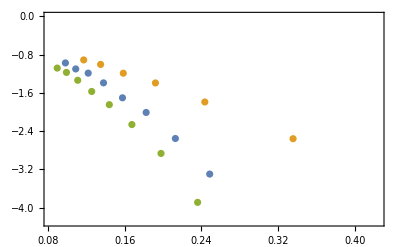

```mathematica
Show[ListPlot[{Table[{Nf0α3LoopMid[[i]],Nf0α3LoopΔEqqbarMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopBig[[i]],Nf0α3LoopΔEqqbarBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopSmall[[i]],Nf0α3LoopΔEqqbarSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

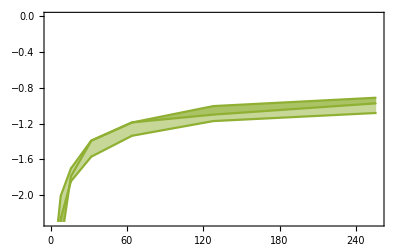

```mathematica
Nf0α3LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqbarMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqbarBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqbarSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{{0,257},{-2.3,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

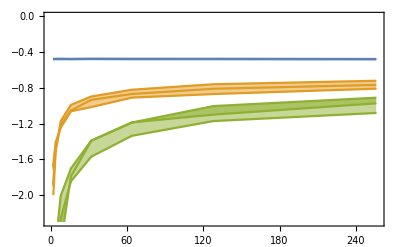

```mathematica
Show[Nf0α3LoopΔEqqbarPlot,Nf0α2LoopΔEqqbarPlot,Nf0α1LoopΔEqqbarPlot]
```

### M_QQQ

#### LO

```mathematica
Nf0α1LoopMid
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopBig]}]
```

{-0.459130.00032,-0.156840.00011,-0.073830.00006,-0.0413380.000029,-0.0258190.000016,-0.0173920.000010,-0.0123688,-0.0092266}

```mathematica
Nf0α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopMid]}]
```

{-0.095390.00011,-0.054550.00007,-0.0338120.000033,-0.0225040.000018,-0.0156540.000013,-0.0114299,-0.0086656,-0.0067494}

```mathematica
Nf0α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopSmall]}]
```

{-0.040120.00005,-0.027360.00004,-0.0193180.000024,-0.0140520.000015,-0.01053410,-0.0081446,-0.0064044,-0.0051524}

```mathematica
ΔEqqqOα2=Nf0α1LoopΔEqqbarMid/Nf0α1LoopMid^2
```

{-0.44444405,-0.44444529,-0.444443514,-0.444443221,-0.444445930,-0.4444474,-0.4444465,-0.4444487}

```mathematica
Nf0α1LoopΔEqqqMid/Nf0α1LoopMid^2
```

{-0.47590.0006,-0.47680.0006,-0.47610.0005,-0.47760.0004,-0.47480.0004,-0.474830.00035,-0.476310.00030,-0.477090.00032}

```mathematica
ΔEqqqOα2WD=3/2Nf0α1LoopΔEqqbarMid/Nf0α1LoopMid^2
```

{-0.66666607,-0.666667913,-0.666665321,-0.666664832,-0.6666695,-0.6666716,-0.6666708,-0.6666720.000011}

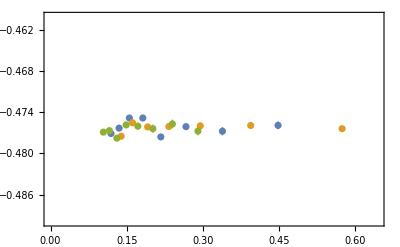

```mathematica
Show[ListPlot[{Table[{Nf0α1LoopMid[[i]],Nf0α1LoopΔEqqqMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopBig[[i]],Nf0α1LoopΔEqqqBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopSmall[[i]],Nf0α1LoopΔEqqqSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{-.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

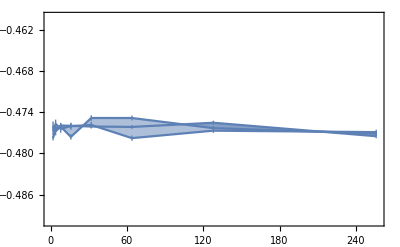

```mathematica
Nf0α1LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{{0,257},{-.49,-.46}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

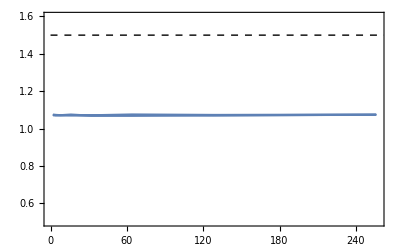

```mathematica
Nf0α1LoopΔEqqbarRatioPlot=Show[ListPlot[{Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqMid[[i]]/Nf0α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqBig[[i]]/Nf0α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqSmall[[i]]/Nf0α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

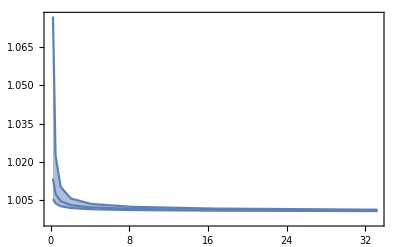

```mathematica
Nf0α1LoopΔEqqbarVsPlot23=Show[ListPlot[{Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],2/3(3+Nf0α1LoopΔEqqqMid[[i]])/(2+Nf0α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf0α1LoopMid]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],2/3(3+Nf0α1LoopΔEqqqBig[[i]])/(2+Nf0α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf0α1LoopBig]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],2/3(3+Nf0α1LoopΔEqqqSmall[[i]])/(2+Nf0α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3)M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

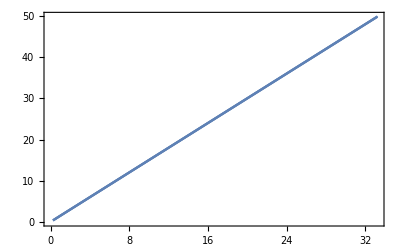

```mathematica
Nf0α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],(3Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqqMid[[i]]Nf0α1LoopmQ[[i]])},{i,1,Length[Nf0α1LoopMid]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],(3Nf0α1LoopmQ[[i]]+Nf0α1LoopmQ[[i]]Nf0α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α1LoopBig]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],(3Nf0α1LoopmQ[[i]]+Nf0α1LoopmQ[[i]]Nf0α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

#### NLO

```mathematica
Nf0α2LoopMid
```

{0.385835,0.281843,0.218714,0.177603,0.149071,0.128222,0.112361,0.0999055}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf0α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopBig]}]
```

{-5.5450.015,-0.63300.0034,-0.17010.0007,-0.072310.00027,-0.039080.00014,-0.023760.00006,-0.015900.00004,-0.0112840.000025}

```mathematica
Nf0α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopMid]}]
```

{-0.3470.004,-0.14210.0013,-0.07240.0006,-0.040230.00023,-0.025090.00015,-0.017400.00008,-0.012060.00006,-0.0089870.000033}

```mathematica
Nf0α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopSmall]}]
```

{-0.10790.0016,-0.06500.0008,-0.03920.0004,-0.025450.00022,-0.017890.00014,-0.012980.00008,-0.009670.00005,-0.007580.00004}

```mathematica
ΔEqqqOα2=Nf0α2LoopΔEqqbarMid/Nf0α2LoopMid^2
```

{-1.8800.020,-1.4830.015,-1.2150.011,-1.0520.008,-0.9340.006,-0.8680.004,-0.80970.0033,-0.76610.0030}

```mathematica
Nf0α2LoopΔEqqqMid/Nf0α2LoopMid^2
```

{-2.3280.024,-1.7880.016,-1.5130.012,-1.2750.007,-1.1290.007,-1.0580.005,-0.9550.004,-0.90040.0033}

```mathematica
ΔEqqqOα2WD=3/2Nf0α2LoopΔEqqbarMid/Nf0α2LoopMid^2
```

{-2.8200.030,-2.2250.022,-1.8220.016,-1.5790.011,-1.4010.009,-1.3020.006,-1.2140.005,-1.1490.004}

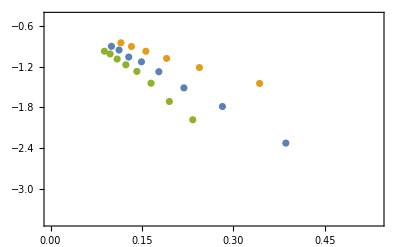

```mathematica
Show[ListPlot[{Table[{Nf0α2LoopMid[[i]],Nf0α2LoopΔEqqqMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopBig[[i]],Nf0α2LoopΔEqqqBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopSmall[[i]],Nf0α2LoopΔEqqqSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

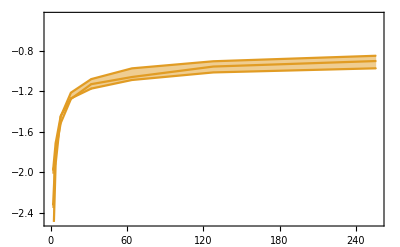

```mathematica
Nf0α2LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

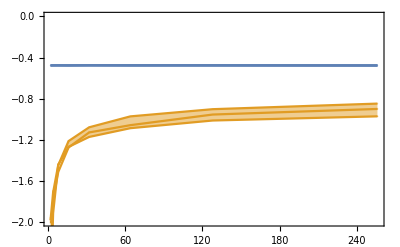

```mathematica
Show[Nf0α2LoopΔEqqbarPlot,Nf0α1LoopΔEqqbarPlot,PlotRange->{-2.0,0},Axes->False]
```

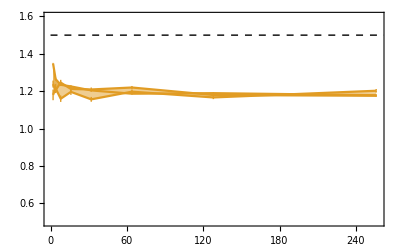

```mathematica
Nf0α2LoopΔEqqbarRatioPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqMid[[i]]/Nf0α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqBig[[i]]/Nf0α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqSmall[[i]]/Nf0α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

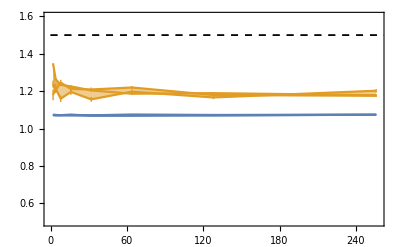

```mathematica
Show[Nf0α2LoopΔEqqbarRatioPlot,Nf0α1LoopΔEqqbarRatioPlot]
```

```mathematica
Series[(3+1.2 ΔEqqbarOα2Exact αα^2)/(2+ΔEqqbarOα2Exact αα^2),{αα,0,2}]
```

3/2+0.0666667 αα^2+O[αα]^3

```mathematica
ΔEqqbarOα2Exact .2^2
```

-0.0177778

```mathematica
Nf5α1LoopΔEqqbarMid
```

{-0.0063882710,-0.0066391010,-0.0069526710,-0.0073629010,-0.0079372710,-0.0088400110,-0.0106435010,-0.0206516110}

```mathematica
Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-0.444442622,-0.444446221,-0.444446220,-0.444446218,-0.444444517,-0.444445816,-0.444444214,-0.444445212}

```mathematica
Nf4α1LoopΔEqqbarMid
```

{-0.0206516110,-0.0216219410,-0.0227788610,-0.0241904110,-0.0259641710,-0.0282833910,-0.0314892110,-0.0363113410}

```mathematica
ΔEqqbarOα2Exact Nf4α1LoopMid^2
```

{-0.0206517,-0.0216219,-0.0227788,-0.0241903,-0.0259642,-0.0282833,-0.0314892,-0.0363113}

```mathematica
Nf4α1LoopMid
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

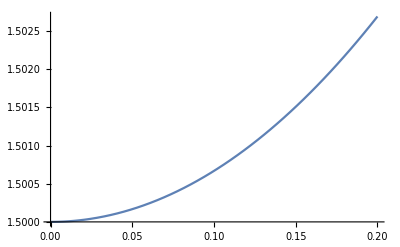

```mathematica
Plot[(3+1.2ΔEqqbarOα2Exact αα^2)/(2+ΔEqqbarOα2Exact αα^2),{αα,0,.2}]
```

```mathematica
(3Nf5α2LoopmQ+Nf5α2LoopΔEqqqMid)/(2Nf5α2LoopmQ+Nf5α2LoopΔEqqbarMid Nf5α2LoopmQ[[i]])
```

```mathematica
Nf5α2LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqBig[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqSmall[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf5α2LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3+Nf5α2LoopΔEqqqMid[[i]])/(2+Nf5α2LoopΔEqqbarMid[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3+Nf5α2LoopΔEqqqBig[[i]])/(2+Nf5α2LoopΔEqqbarBig[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3+Nf5α2LoopΔEqqqSmall[[i]])/(2+Nf5α2LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

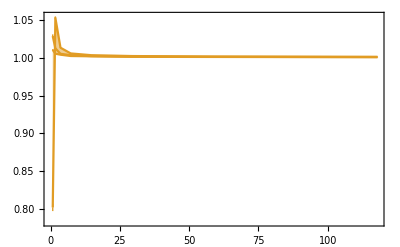

```mathematica
Nf0α2LoopΔEqqbarVsPlot23=Show[ListPlot[{Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqMid[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqBig[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarBig[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqSmall[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarSmall[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

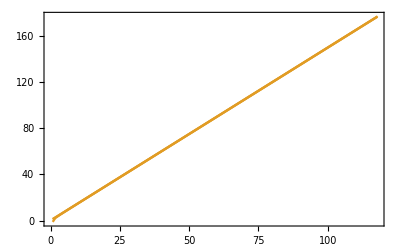

```mathematica
Nf0α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqMid[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmQ[[i]]Nf0α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmQ[[i]]Nf0α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

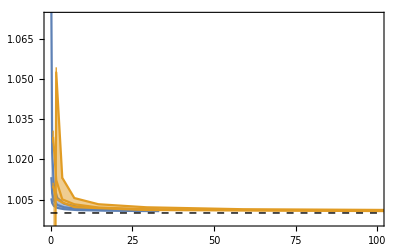

```mathematica
Show[Nf0α1LoopΔEqqbarVsPlot23,Nf0α2LoopΔEqqbarVsPlot23,Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{0,100},{2/3 1.495,2/3 1.61}},Axes->False]
```

#### NNLO

```mathematica
Nf0α3LoopMid
```

{0.24869,0.212846,0.182354,0.157659,0.137848,0.121869,0.108843,0.098095}

```mathematica
Nf0α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-2.1350.006,-0.37630.0014,-0.13740.0005,-0.064770.00023,-0.036000.00012,-0.022560.00006,-0.015180.00004}

```mathematica
Nf0α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopMid]}]
```

{-0.25280.0022,-0.14040.0012,-0.08500.0005,-0.050730.00031,-0.033310.00020,-0.022450.00011,-0.015910.00006,-0.011900.00005}

```mathematica
Nf0α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopSmall]}]
```

{-0.27770.0028,-0.14620.0014,-0.08110.0007,-0.04790.0004,-0.029620.00023,-0.020730.00014,-0.014280.00008,-0.010440.00005}

```mathematica
ΔEqqqOα2=Nf0α3LoopΔEqqbarMid/Nf0α3LoopMid^2
```

{-3.2990.032,-2.5540.024,-2.0090.015,-1.7030.011,-1.3900.008,-1.1860.007,-1.0990.005,-0.9730.004}

```mathematica
Nf0α3LoopΔEqqqMid/Nf0α3LoopMid^2
```

{-4.0880.035,-3.0990.026,-2.5550.017,-2.0410.013,-1.7530.011,-1.5110.007,-1.3430.005,-1.2360.005}

```mathematica
ΔEqqqOα2WD=3/2Nf0α3LoopΔEqqbarMid/Nf0α3LoopMid^2
```

{-4.950.05,-3.830.04,-3.0140.023,-2.5540.017,-2.0850.011,-1.7790.010,-1.6480.008,-1.4590.006}

```mathematica
Show[ListPlot[{Table[{Nf0α3LoopMid[[i]],Nf0α3LoopΔEqqqMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopBig[[i]],Nf0α3LoopΔEqqqBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopSmall[[i]],Nf0α3LoopΔEqqqSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{-14.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{{0,257},{-2.49,-.46}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nf0α3LoopΔEqqbarPlot,Nf0α2LoopΔEqqbarPlot,Nf0α1LoopΔEqqbarPlot,PlotRange->{-2.49,0}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqbarRatioPlot=Show[ListPlot[{Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqMid[[i]]/Nf0α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqBig[[i]]/Nf0α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqSmall[[i]]/Nf0α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf0α3LoopΔEqqbarRatioPlot,Nf0α2LoopΔEqqbarRatioPlot,Nf0α1LoopΔEqqbarRatioPlot]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqbarVsPlot23=Show[ListPlot[{Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],2/3(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqMid[[i]]Nf0α3LoopmQ[[i]])/(2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopMid]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],2/3(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqBig[[i]]Nf0α3LoopmQ[[i]])/(2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarBig[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopBig]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],2/3(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqSmall[[i]]Nf0α3LoopmQ[[i]])/(2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarSmall[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqMid[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopMid]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],(3Nf0α3LoopmQ[[i]]+Nf0α3LoopmQ[[i]]Nf0α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α3LoopBig]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],(3Nf0α3LoopmQ[[i]]+Nf0α3LoopmQ[[i]]Nf0α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-